```mathematica
?PadeApproximant
```

```mathematica
PadeApproximant[Cos[x],{x,0,{n,m}}]
```

(1-(7 x^2)/15+x^4/40)/(1+x^2/30)

```mathematica
PadeApproximant[Cos[x],{x,0,{4,3}}]
```

(1-(7 x^2)/15+x^4/40)/(1+x^2/30)

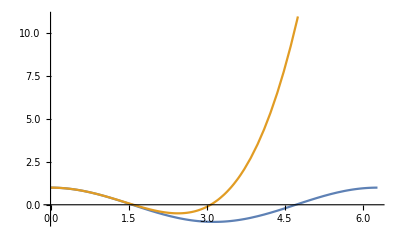

```mathematica
Plot[{Cos[x],PadeApproximant[Cos[x],{x,0,{4,0}}]//Evaluate},{x,0,2π}]
```

## Step by step solution

```mathematica
Clear[f,n,m,eters,q,p,a,sol,equations]
f[x_]=Cos[x];
n=4;
m = 2;
eters = n+m+1;
q[0]=1;
Do[a[i]=(Derivative[i][f][0])/(i!),{i,0,eters}]
Do[p[i]=0,{i,n+1,eters}]
Do[q[i]=0,{i,m+1,eters}]
equations = Table[Sum[a[i]q[k-i],{i,0,k}]==p[k],{k,0,eters-1}];
vars ={Table[q[i],{i,1,m}],Table[p[i],{i,0,n}]}//Flatten;
sol = Solve[equations,vars]//Flatten;
Q[x_]=Sum[p[i] x^i,{i,0,n}]/Sum[q[i] x^i,{i,0,m}]/.sol
```

(1-(7 x^2)/15+x^4/40)/(1+x^2/30)

```mathematica
equations//TableForm//TraditionalForm
```

1==p(0)
q(1)==p(1)
q(2)-1/2==p(2)
-(q(1))/2==p(3)
1/24-(q(2))/2==p(4)
(q(1))/24==0
(q(2))/24-1/720==0